## Evaluating the components of the Energy Function

```mathematica
ClearAll["Global`*"]
```

```mathematica
tcore[I_,A1_,A2_,A3_]:=I/2(A1+A2)+A3*I^2;
tsp[j_,A1_,A2_,A3_,V_,gm_]:=j/2(A2+A3)+A1*j^2-V*(2j-1)/(j+1)Sin[gm*π/180+π/6];
```

```mathematica
A11=1/(2*10);A21=1/(2*20);A31=1/(2*45);
A12=1/(2*45);A22=1/(2*10);A32=1/(2*20);
A13=1/(2*45);A23=1/(2*20);A33=1/(2*10);
j1=13/2;j2=11/2;j3=9/2;
Vfit=2.1;
gmfit=22;
moiW2={72,15,7};
A1W2=1/(2*moiW2[[1]]);
A2W2=1/(2*moiW2[[2]]);
A3W2=1/(2*moiW2[[3]]);
```

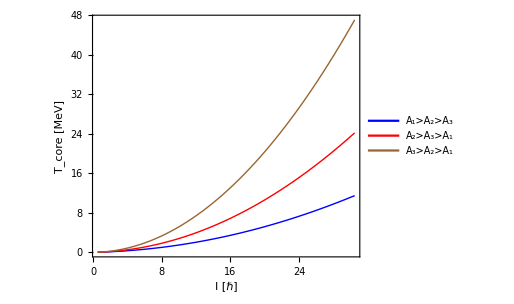

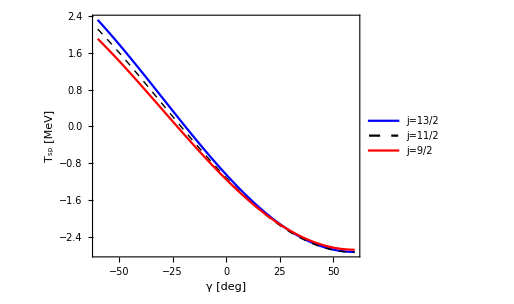

```mathematica
coreplot=Plot[{tcore[x,A11,A21,A31],tcore[x,A12,A22,A32],tcore[x,A13,A23,A33]},{x,0.5,30.5},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],ImageSize->380,AspectRatio->0.8,PlotRange->Full,FrameLabel->{"I [ℏ]","T_core [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotStyle->{{Blue,Thick},{Red,Thick},{Brown,Thick}},PlotLegends->Placed[{"A_1>A_2>A_3","A_2>A_3>A_1","A_3>A_2>A_1"},{0.3,0.7}]];Show[coreplot]
Export["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/t-core.pdf",Show[coreplot]];
spplot=Plot[{tsp[j1,A1W2,A2W2,A3W2,Vfit,x],tsp[j2,A1W2,A2W2,A3W2,Vfit,x],tsp[j3,A1W2,A2W2,A3W2,Vfit,x]},{x,-60,60},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],ImageSize->380,AspectRatio->0.8,PlotRange->Full,FrameLabel->{"γ [deg]","T_sp [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotStyle->{{Blue},{Black,Thick,Dashed},{Red}},PlotLegends->Placed[{"j=13/2","j=11/2","j=9/2"},{0.7,0.7}]];Show[spplot]
Export["/Users/basavyr/Documents/Work/PhD/163Lu-New-TSD4-Formalism/Code/Update-July-2022/plots/t-sp.pdf",Show[spplot]];
```

```mathematica
A11=N[1/(2*10)]
A21=N[1/(2*20)]
A31=N[1/(2*45)]
A12=1/(2*45);A22=1/(2*10);A32=1/(2*20);
A13=1/(2*45);A23=1/(2*20);A33=1/(2*10);
```

0.05

0.025

0.0111111

```mathematica
N[A31]
```

0.0111111